# Sharp bubble for the Alcubierre drive

## Exact smooth top-hat function

```mathematica
(*https://www.j-raedler.de/2010/10/smooth-transition-between-functions-with-tanh*)
(*https://en.wikipedia.org/wiki/Non-analytic_smooth_function#Smooth_transition_functions*)
ClearAll[SNAf,SNAg,SNAh];
SNAf[x_]:=Piecewise[{{Exp[-1/x],x>0},{0,x≤0}}];
SNAg[x_]:=SNAf[x]/(SNAf[x]+SNAf[1-x]);
SNAh[xa_,xb_,x_]:=SNAg[(x-xa)/(xb-xa)];

ClearAll[T];
T[a_,xa_,b_,xb_,x_]:=b*SNAh[xa,xb,x]+(1-SNAh[xa,xb,x])a;

ClearAll[TopHat];
TopHat[σ_,R_,x_]:=T[0,-σ,1,-R,x]T[0,σ,1,R,x];

ClearAll[r];
r[t_,x_,y_,z_]:=Sqrt[(x-v*t)^2+y^2+z^2];
```

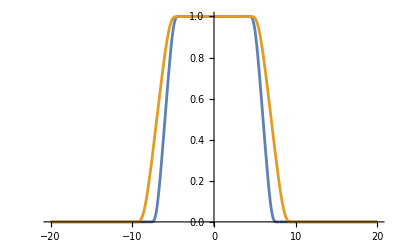

```mathematica
Plot[
{
TopHat[8,4,x],
TopHat[10,4,x]
},
{x,-20,20},
PlotRange->Full
]
```

## Volume elements

### Exact smooth Tophat

```mathematica
ClearAll[expansion];
expansion=v*D[TopHat[8,4,r[0,x,y,0]],x]//.{v->1/2};

Plot3D[
expansion,
{x,-10,10},
{y,-10,10},
PlotPoints->100,
PlotRange->Full,
Exclusions->None,
AxesLabel->{"x","y","θ"}
]

ClearAll[expansion];
```

-Graphics3D-

### Steve’s deflector shield component

```mathematica
ClearAll[ρ];
ρ[y_,z_]:=y/Sqrt[y^2+z^2];

ClearAll[vx,vy,expansion];
vx=TopHat[σx,Rx,r[t,x,y,z]];
vy=k*ρ[y,z]TopHat[σy,Ry,r[t,x,y,z]];

expansion=(D[vx,x]+D[vy,y])//.{t->0,z->0,Rx->4,σx->2Rx,Ry->Rx,σy->3Rx,k->1/2,v->1/2};

Plot3D[expansion,{x,-20,20},{y,-20,20},PlotPoints->100,Exclusions->None,PlotRange->Full]

ClearAll[vx,vy,expansion];
ClearAll[ρ];
```

-Graphics3D-

## Quantities

```mathematica
ClearAll[th,dth];

th=FullSimplify[
TopHat[sigma,radius,rr],
{
sigma∈Reals,
radius∈Reals,
rr∈Reals,
sigma>=0,
radius>=0,
rr>=0,
sigma>radius
}
];

dth=FullSimplify[
D[th,rr],
{
sigma∈Reals,
radius∈Reals,
rr∈Reals,
sigma>=0,
radius>=0,
rr>=0,
sigma>radius
}
];
```

```mathematica
Print[th]
Print[dth]
```

Piecewise[{{1/(1+ⅇ^(((radius-sigma) (radius-2 rr+sigma))/((radius-rr) (rr-sigma)))), radius<rr&&rr<sigma}, {0, radius<rr}, {1, True}}]

Piecewise[{{((radius-sigma) (radius^2-2 radius rr+2 rr^2-2 rr sigma+sigma^2) Sech[((radius-sigma) (radius-2 rr+sigma))/(2 (radius-rr) (rr-sigma))]^2)/(4 (radius-rr)^2 (rr-sigma)^2), radius<rr&&rr<sigma}, {0, True}}]